# Stark broadening

## line emission plot

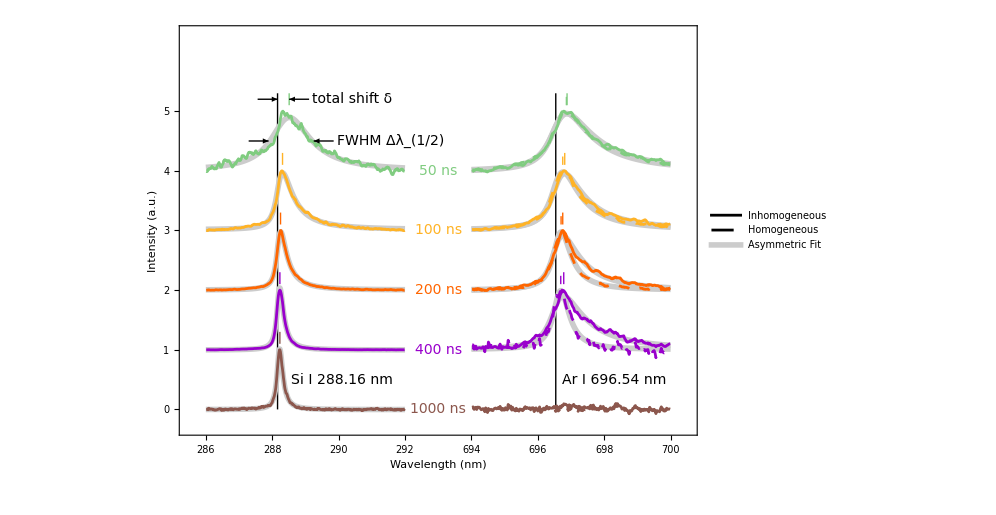

```mathematica
(* -- import data -- *)
nb=NotebookDirectory[];
dt288=Select[#,(286≤#[[1]]≤292&)]&/@Import[nb<>"data/line emission/288norm.mx"];
fdt288=Select[#,(286≤#[[1]]≤292&)]&/@Import[nb<>"data/line emission/"<>"288FitData.mx"];
dt697=Select[#,(694≤#[[1]]≤700&)]&/@Flatten[Import[nb<>"data/line emission/697norm.mx"],1];
fdt697=Select[#,(694≤#[[1]]≤700&)]&/@Flatten[Import[nb<>"data/line emission/"<>"697FitData.mx"],1];

(* -- data correction -- *)
δ=694-292-2;
dt697[[All,All,1]]-=δ;(*wavelength shift*)
fdt697[[All,All,1]]-=δ;(*wavelength shift*)

dt=Flatten[{dt288,dt697},1];
fdt=Flatten[{fdt288,fdt697},1];

(* -- width & shifts -- *)
{peaks,half}=Table[
m=MinMax[fdt[[i,All,2]]];
p=Select[fdt[[i]],(#[[2]]==m[[2]]&)][[1,1]];
h=Part[Select[fdt[[i]],(#[[2]]≥Mean@m&)],{1,-1}];
{p,h[[All,1]]}
,{i,13}]ᵀ;

(* -- plot style -- *)
clr={RGBColor[.5,.8,.5],RGBColor[1,.7,.15],RGBColor[1,.4,0],RGBColor[.6,0,.8],RGBColor[.55,.34,.3]};
ps=Directive@@@Flatten[{
ConstantArray[{RGBColor[.8,.8,.8,1],AbsoluteThickness[4]},13],
{#,AbsoluteThickness[2]}&/@clr,
{#,AbsoluteThickness[2]}&/@clr,
{#,AbsoluteThickness[2],AbsoluteDashing[8]}&/@clr
},1];

(* -- plot -- *)
gf=ListLinePlot[

Flatten[{fdt,dt},1],

Prolog->{
(* Si I 288.16 nm *)
{Black,AbsoluteThickness[1],Line[{{288.16,0},{288.16,5.3}}]},
{Text[Style["Si I 288.16 nm",FontSize->14,FontColor->Black,FontWeight->Plain],{288.16+.4,.5},{-1,0}]},
(* Ar I 696.54 nm *)
{Black,AbsoluteThickness[1],Line[{{696.54-δ,0},{696.54-δ,5.3}}]},
{Text[Style["Ar I 696.54 nm",FontSize->14,FontColor->Black,FontWeight->Plain],{696.54+.2-δ,.5},{-1,0}]}
},

Epilog->{
(* -- shifts -- *)
Table[
{clr[[i]],AbsoluteThickness[1],Line[{{peaks[[i]],6.1-i},{peaks[[i]],6.3-i}}]}
,{i,5}],
Table[
{clr[[i]],AbsoluteThickness[1],Line[{{peaks[[i+5]],6.1-i},{peaks[[i+5]],6.3-i}}]}
,{i,4}],
Table[
{clr[[i]],AbsoluteThickness[1],AbsoluteDashing[6],Line[{{peaks[[i+9]],6.1-i},{peaks[[i+9]],6.3-i}}]}
,{i,4}],
{Black,AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{288.16-.6,5.2},{288.16,5.2}}]},
{Black,AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{peaks[[1]]+.6,5.2},{peaks[[1]],5.2}}]},
Text[Style["total shift δ",{FontColor->Black,FontSize->14,FontWeight->Plain}],{peaks[[1]]+.7,5.2},{-1,0}],
(* -- width -- *)
{Black,AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{half[[1,1]]-.6,4.5},{half[[1,1]],4.5}}]},
{Black,AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{half[[1,2]]+.6,4.5},{half[[1,2]],4.5}}]},
Text[Style["FWHM Δλ_(1/2)",{FontColor->Black,FontSize->14,FontWeight->Plain}],{half[[1,2]]+.7,4.5},{-1,0}],
(* -- delay time label -- *)
Text[Style["50 ns",{FontColor->clr[[1]],FontSize->14,FontWeight->Plain}],{293,4},{0,0}],
Text[Style["100 ns",{FontColor->clr[[2]],FontSize->14,FontWeight->Plain}],{293,3},{0,0}],
Text[Style["200 ns",{FontColor->clr[[3]],FontSize->14,FontWeight->Plain}],{293,2},{0,0}],
Text[Style["400 ns",{FontColor->clr[[4]],FontSize->14,FontWeight->Plain}],{293,1},{0,0}],
Text[Style["1000 ns",{FontColor->clr[[5]],FontSize->14,FontWeight->Plain}],{293,0},{0,0}],
(* axes cutout *)
Inset[
Graphics[{
{White,Polygon[{{-2,-2},{0,-2},{2,2},{0,2}}]},
{Black,AbsoluteThickness[1],Line[{{-2,-2},{0,2}}]},
{Black,AbsoluteThickness[1],Line[{{0,-2},{2,2}}]}
}],
{293,-.3},{0,0},{.3,.3}],
Inset[
Graphics[{
{White,Polygon[{{-2,-2},{0,-2},{2,2},{0,2}}]},
{Black,AbsoluteThickness[1],Line[{{-2,-2},{0,2}}]},
{Black,AbsoluteThickness[1],Line[{{0,-2},{2,2}}]}
}],
{293,6.3},{0,0},{.3,.3}]
},

PlotRange->{{285.5,700.5-δ},{-.3,6.3}},
Joined->True,

PlotStyle->ps,

PlotLegends->
Placed[
LineLegend[
{Directive[Black,AbsoluteThickness[2]],Directive[Black,AbsoluteThickness[2],AbsoluteDashing[8]],Directive[RGBColor[.8,.8,.8,1],AbsoluteThickness[4]]},
{"Inhomogeneous","Homogeneous","Asymmetric Fit"},
LegendMarkerSize->{{60,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Row",1}
],
{{.5,.95},{.5,1}}],

Axes->False,
Frame->True,
FrameLabel->{{"Intensity (a.u.)",None},{"Wavelength (nm)",None}},
FrameTicks->{
{Table[{i,i,{.015,0}},{i,0,5,1}],Table[{i,Null,{.015,0}},{i,0,5,1}]},
{Table[{i,If[i≤293,i,i+δ],{.015,0}},{i,286,701-δ,2}],Table[{i,Null,{.015,0}},{i,286,701-δ,2}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,

PlotRangeClipping->False,
ImagePadding->{{35,5},{45,10}},
ImageSize->(130*2)*(72/25.4),
AspectRatio->.7

];

Print[gf];

Export[NotebookDirectory[]<>"fit.pdf",gf];
```

## density estimation

```mathematica
(* -- import data -- *)
nb=NotebookDirectory[];
temperatureRaw=Import[nb<>"data/continuum/coreFitParameters.mx"][[All,All,2]];
parameters={
{Import[nb<>"data/line emission/288FitParameters.mx"]}, (* Si *)
Import[nb<>"data/line emission/697FitParameters.mx"] (* Ar *)
};

(* -- temperature extrapolation -- *)
time={1,5,10,20,50,100,200,400,1000};
temperatureFunc=Table[nlm=NonlinearModelFit[{time[[;;7]],temperatureRaw[[i]]}ᵀ,a x^b+c,{{a,1000},{b,-.1},{c,1000}},x],{i,2}];
temperature=Table[temperatureFunc[[i]][#]&/@time,{i,2}];

(* -- paramters -- *)
dTot=parameters[[All,All,All,-2]];
wTot=parameters[[All,All,All,-1]];

(* -- density -- *)
neFunc[δ_,t_,{δRef_,tRef_,nRef_}]:=nRef(δ/δRef)√(t/tRef);
ref=<|
"Si"-><|
"w"-><|"Konjevic2002"->{.054,28500,1.9*^17}|>,
"d"-><|"Konjevic2002"->{.020,28500,1.9*^17}|>
|>,
"Ar"-><|
"w"-><|"Konjevic2002"->{.04,11900,.6*^17}|>,
"d"-><|"Konjevic2002"->{.01,13000,.33*^17}|>
|>
|>;

ne={
Map[MeanAround,
{neFunc[wTot[[1,1,;;-2]],temperature[[1,-5;;-2]],ref["Si"]["w"]["Konjevic2002"]],
neFunc[dTot[[1,1,;;-2]],temperature[[1,-5;;-2]],ref["Si"]["d"]["Konjevic2002"]],
neFunc[wTot[[2,1]],temperature[[1,-5;;-2]],ref["Ar"]["w"]["Konjevic2002"]],
neFunc[dTot[[2,1]],temperature[[1,-5;;-2]],ref["Ar"]["d"]["Konjevic2002"]]}ᵀ],
Map[MeanAround,
{neFunc[wTot[[2,2]],temperature[[1,-5;;-2]],ref["Ar"]["w"]["Konjevic2002"]],
neFunc[dTot[[2,2]],temperature[[1,-5;;-2]],ref["Ar"]["d"]["Konjevic2002"]]}ᵀ]
};
neLast=Around[Mean[#],Apply[Subtract,#]/2]&/@{{neFunc[wTot[[1,1,-1]],temperature[[1,-1]],ref["Si"]["w"]["Konjevic2002"]],
neFunc[dTot[[1,1,-1]],temperature[[1,-1]],ref["Si"]["d"]["Konjevic2002"]]}};
AppendTo[ne[[1]],neLast[[1,1]]];

dt={{time[[-5;;]],ne[[1]]/10^18}ᵀ,{time[[-5;;-2]],ne[[2]]/10^18}ᵀ};

(* -- plot -- *)
gf=ListLinePlot[

dt,

(*Epilog->{
(* -- panel label -- *)
Text[Style["b",{FontColor->Black,FontSize->25,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},*)

PlotRange->{{40,1200},{0,2.5}},
Joined->True,
ScalingFunctions->{"Log","Linear"},

PlotStyle->{
Directive[Black,AbsoluteThickness[1.5]],
Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]
},

PlotMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},

IntervalMarkers->"Fences",
IntervalMarkersStyle-><|
"FenceStyle"->{
Directive[AbsoluteThickness[1],"LineOpacity"->1,"LineColor"->Black,"Dashing"->None],
Directive[AbsoluteThickness[1],"LineOpacity"->1,"LineColor"->Black,"Dashing"->None]
},
"WhiskerStyle"->{
Directive[AbsoluteThickness[1],"LineOpacity"->1,"LineColor"->Black,"Dashing"->None],
Directive[AbsoluteThickness[1],"LineOpacity"->1,"LineColor"->Black,"Dashing"->None]
}
|>,

PlotLegends->
Placed[
LineLegend[
{Directive[Black,AbsoluteThickness[1.5]],Directive[Black,AbsoluteThickness[1.5],AbsoluteDashing[4]]},
{"Inhomogeneous","Homogeneous"},
LegendMarkers->{
{Graphics[{
FaceForm[Lighter@Purple,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Disk[]},PlotRangePadding->0],Offset[10]},
{Graphics[{
FaceForm[Darker@Cyan,Opacity[1]],
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1.5]}],
Rectangle[]},PlotRangePadding->0],Offset[10]}
},
LegendMarkerSize->{{40,10}},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMargins->1,LegendLayout->{"Column",1}
],
{{.97,.92},{1,1}}],

Axes->False,
Frame->True,
FrameLabel->{{"Electron density (10^18 cm^-3)",None},{"Time (ns)",None}},
FrameTicks->{
{Table[{i,If[FractionalPart@i==0,IntegerPart@i,Null],{If[FractionalPart@i==0,.015,.008],0}},{i,0,3,.5}],
Table[{i,Null,{If[FractionalPart@i==0,.015,.008],0}},{i,0,3,.5}]},
{Table[{i,If[MemberQ[time,i],i,Null],{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}],Table[{i,Null,{If[FractionalPart[Log10@i]==0,.015,.008],0}},{i,Union@Flatten@Table[m n,{m,Range[10]},{n,PowerRange[1,1000,10]}]}]}
},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

LabelStyle->{FontColor->Black,FontFamily->"Arial",FontSize->14,FontWeight->Plain},

GridLines->None,
GridLinesStyle->{{Gray,AbsoluteThickness[1]},{Gray,AbsoluteThickness[1]}},

PlotRangeClipping->False,
ImagePadding->{{35,5},{40,5}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.5

];

Print[gf];

(* -- export -- *)
Export[NotebookDirectory[]<>"density.pdf",gf];
```

-Graphics-